For lab 4 I need to complete exercises 1 and 3

```mathematica
f[x_,y_]=2 y ⅇ^(-x^2-y^2)
Plot3D[f[x,y],{x,-1,3},{y,-2,2},Boxed->False, AxesLabel->{x,y,z}]
```

2 ⅇ^(-x^2-y^2) y

-Graphics3D-

```mathematica
f[x_,y_]=2y*Exp[-x^2-y^2];
surface=Plot3D[f[x,y],{x,-1,3},{y,-2,2},Boxed->False,PlotStyle->Directive[Opacity[0.5]],PlotRange->All,Mesh->15];
point={RGBColor[0,1,0],PointSize[0.03],Point[{1,0,0}]};
n=22;
rmin=-2;rmax=2;
dr=(rmax-rmin)/n;
section={RGBColor[0,0,1],Thickness[0.01],Table[Line[{{1+r Cos[t],r Sin[t],2 r Sin[t] ⅇ^(-1-r^2-2 r Cos[t])},{1+(r+dr) Cos[t],(r+dr) Sin[t],2 (r+dr) Sin[t] ⅇ^(-1-(r+dr)^2-2 (r+dr) Cos[t])}}],{r,rmin,rmax-dr,dr}]};
plane={RGBColor[0,0,1],Thickness[0.01],Line[{{1+rmax Cos[t],rmax Sin[t],2 rmax Sin[t] ⅇ^(-1-rmax^2-2 rmax Cos[t])},{1+rmax Cos[t],rmax Sin[t],-1.5},{1-rmax Cos[t],-rmax Sin[t],-1.5},{1-rmax Cos[t],-rmax Sin[t],2 (-rmax) Sin[t] ⅇ^(-1-rmax^2+2 rmax Cos[t])}}]};
gf[x_,y_]={D[f[x,y], x],D[f[x,y], y]};
vector={RGBColor[1,0,0],Thickness[0.01],Arrow[{{1-Cos[t],-Sin[t],-(2 Sin[t])/ⅇ},{1+1 Cos[t],1 Sin[t],(2 Sin[t])/ⅇ}}]};
g[t_]=Graphics3D[{point,vector,section,plane},Boxed->False,PlotRange->{{-1,3.15},{-3,2},{-1.5,1}},ViewPoint->{2,-3,1.5}];

Manipulate[Show[g[t],surface],{{t,0,"Bearing"},0,2Pi}]
```

```mathematica
f[x_,y_]=x^2+y^2-z
Grad[f[x,y], {x,y}]
```

x^2+y^2-z

{2 x,2 y}

```mathematica
f[x_,y_]=2y*Exp[-x^2-y^2]
```

2 ⅇ^(-x^2-y^2) y

```mathematica
u={3,4}/Sqrt[3^2+4^2]
```

{3/5,4/5}

```mathematica
unitvec[v_]=v/Norm[v]
```

v/Norm[v]

```mathematica
u=unitvec[{3,4}]
```

{3/5,4/5}

```mathematica
gradf[x_,y_]=Grad[f[x,y], {x,y}]
```

{-4 ⅇ^(-x^2-y^2) x y,2 ⅇ^(-x^2-y^2)-4 ⅇ^(-x^2-y^2) y^2}

```mathematica
gradf[1,0]
```

{0,2/ⅇ}

```mathematica
u
gradf[1,0].u
```

{3/5,4/5}

8/(5 ⅇ)

```mathematica
u=unitvec[{-1,2}]
gradf[1,0].u
N[%]
```

{-1/(√5),2/(√5)}

4/(√5 ⅇ)

0.658083

```mathematica
u=unitvec[{-1,-1}]
gradf[1,0].u
N[%]
```

{-1/(√2),-1/(√2)}

-(√2)/ⅇ

-0.52026

```mathematica
ClearAll
```

ClearAll

Start of exercise 1***

```mathematica
T(x_,y_,z_)=6000/(1+(x^2+y^2+z^2)/5)
```

6000/(1+1/5 (x^2+y^2+z^2))

```mathematica
u=unitvec[{-4,-3,5}]
```

{-(2 √2)/5,-3/(5 √2),1/(√2)}

```mathematica
gradt[x_,y_,z_]=Grad[T[x,y,z], {x,y,z}]
```

{-(2400 x)/((1+1/5 (x^2+y^2+z^2))^2),-(2400 y)/((1+1/5 (x^2+y^2+z^2))^2),-(2400 z)/((1+1/5 (x^2+y^2+z^2))^2)}

```mathematica
gradt[9,2,1].u
N[%]
```

(222000 √2)/8281

37.9127

The directional derivative of T(x,y,z) at point (9,2,1) in the direction of (-4,3,5)
is equal to 37.9127
End of exercise 1***

```mathematica
ClearAll
```

ClearAll

```mathematica
F[x_,y_]={-y,x}
```

{-y,x}

```mathematica
F[2,1]
```

{-1,2}

```mathematica
F[0,0]
F[1,0]
F[2,0]
F[0,1]
F[1,1]
F[2,1]
F[0,2]
F[1,2]
F[2,2]
```

{0,0}

{0,1}

{0,2}

{-1,0}

{-1,1}

{-1,2}

{-2,0}

{-2,1}

{-2,2}

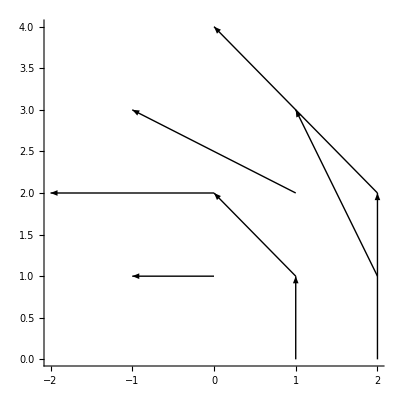

```mathematica
Show[Graphics[{Arrow[{{0,0},{0,0}}],Arrow[{{1,0},{1,1}}],Arrow[{{2,0},{2,2}}],Arrow[{{0,1},{-1,1}}],Arrow[{{1,1},{0,2}}],Arrow[{{2,1},{1,3}}],Arrow[{{0,2},{-2,2}}],Arrow[{{1,2},{-1,3}}],Arrow[{{2,2},{0,4}}]}],Axes->True,AspectRatio->Automatic]
```

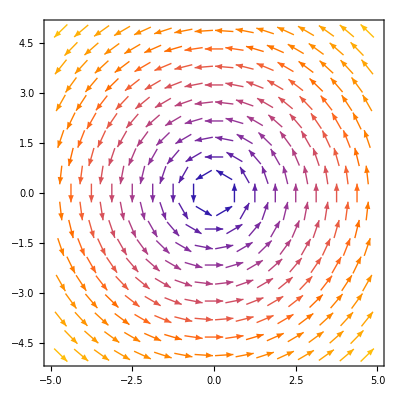

```mathematica
VectorPlot[{-y,x},{x,-5,5},{y,-5,5}];
Show[%,Axes->True]
```

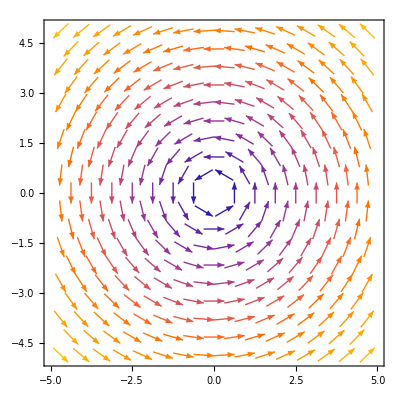

```mathematica
VectorPlot[{-y,x},{x,-5,5},{y,-5,5},VectorScale-> .05]
```

```mathematica
ClearAll
```

ClearAll

{-x,-y}

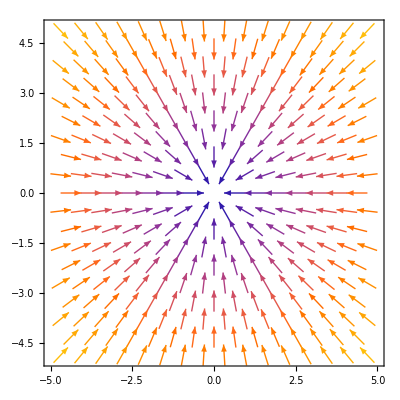

```mathematica
F[x_,y_]={-x,-y}
VectorPlot[F[x,y],{x,-5,5},{y,-5,5},VectorScale->.05]
```

{-y/(x^2+y^2),x/(x^2+y^2)}

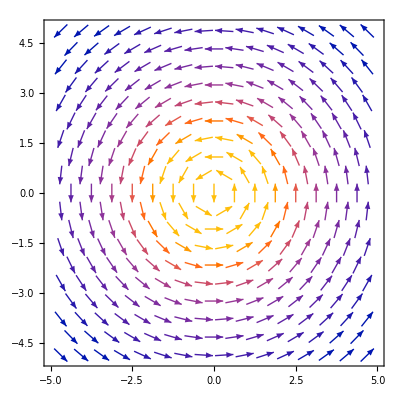

```mathematica
F[x_,y_]={-y/(x^2+y^2),x/(x^2+y^2)}
VectorPlot[F[x,y],{x,-5,5},{y,-5,5},VectorPoints->16]
```

{1,Sin[x]}

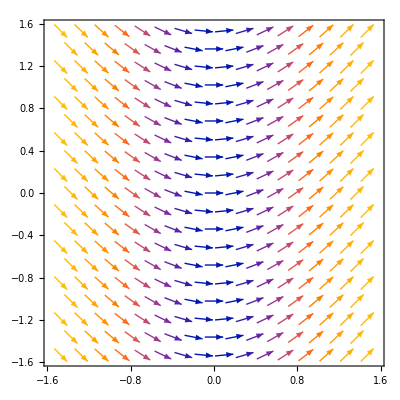

```mathematica
F[x_,y_]={1,Sin[x]}
VectorPlot[F[x,y],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2}]
```

```mathematica
F[x_,y_,z_]={-y,x,z}
VectorPlot3D[F[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5}]
```

{-y,x,z}

-Graphics3D-

```mathematica
F[x_,y_,z_]={-y,x,z}
VectorPlot3D[F[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},VectorStyle->"Segment"]
```

{-y,x,z}

-Graphics3D-

```mathematica
F[x_,y_,z_]={0,0,-9.8}
VectorPlot3D[F[x,y,z],{x,-50,50},{y,-50,50},{z,0,50},VectorStyle->"Segment",VectorPoints -> 16]
```

{0,0,-9.8}

x y

{y,x}

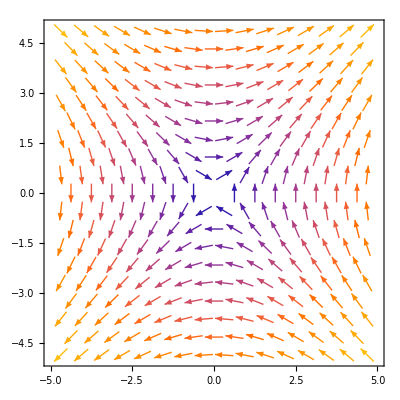

```mathematica
f[x_,y_]=x*y
gradf[x_,y_]=Grad[f[x,y], {x,y}]
gradfieldpic=VectorPlot[gradf[x,y],{x,-5,5},{y,-5,5}]
```

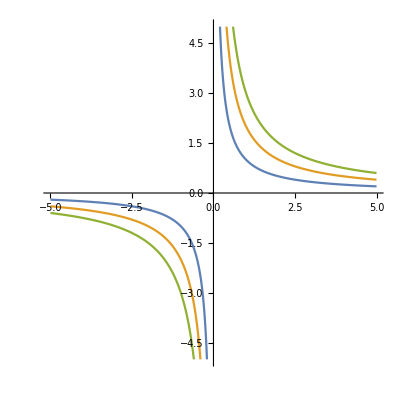

```mathematica
Plot[{1/x,2/x,3/x},{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic]
```

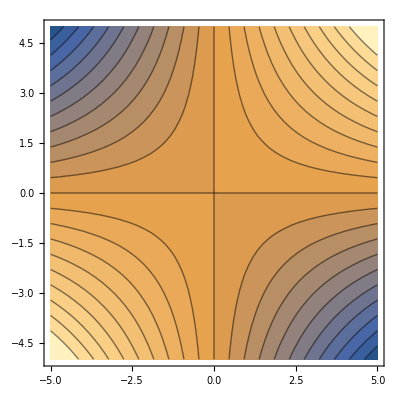

```mathematica
contourpic=ContourPlot[f[x,y],{x,-5,5},{y,-5,5},Contours->20]
```

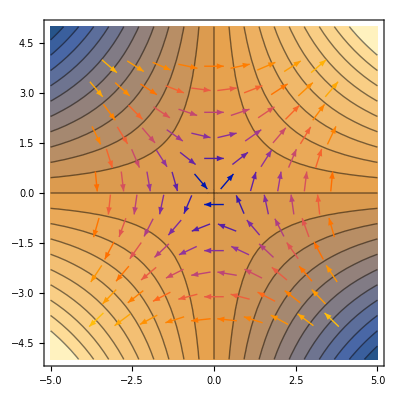

```mathematica
gradfieldpic=VectorPlot[gradf[x,y],{x,-4,4},{y,-4,4},VectorPoints->10];
Show[contourpic,gradfieldpic]
```

Start of exercise 3

```mathematica
ClearAll
```

ClearAll

```mathematica
T[x_,y_,z_]=(6000/(1+(x^2+y^2+z^2)/5))
```

6000/(1+1/5 (x^2+y^2+z^2))

```mathematica
gradt[x_,y_,z_]=Grad[T[x,y,z], {x,y,z}]
```

{-(2400 x)/((1+1/5 (x^2+y^2+z^2))^2),-(2400 y)/((1+1/5 (x^2+y^2+z^2))^2),-(2400 z)/((1+1/5 (x^2+y^2+z^2))^2)}

```mathematica
gradt[9,2,1]
```

{-540000/8281,-120000/8281,-60000/8281}

```mathematica
N[%]
```

{-65.2095,-14.491,-7.2455}

```mathematica
gradfieldpic=VectorPlot3D[gradt[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

Question:In what direction is the largest increase in temperature? 
Answer: the largest increase in temperature would be in the direction of the origin/ sun, this isn’t the least bit surprising, because it is obvious that temperature would increase as we get closer to the sun.
Question:In which direction could the spaceship go to remain at the same temperature? 
Answer: to remain at the same temperature you would have to remain on the level set, since the gradient is in the direction perpendicular to the level set and you want to stay parallel with it, we cant just follow the gradient. we would have to travel along the direction orthogonal to the negative gradient of T at (9,2,1)